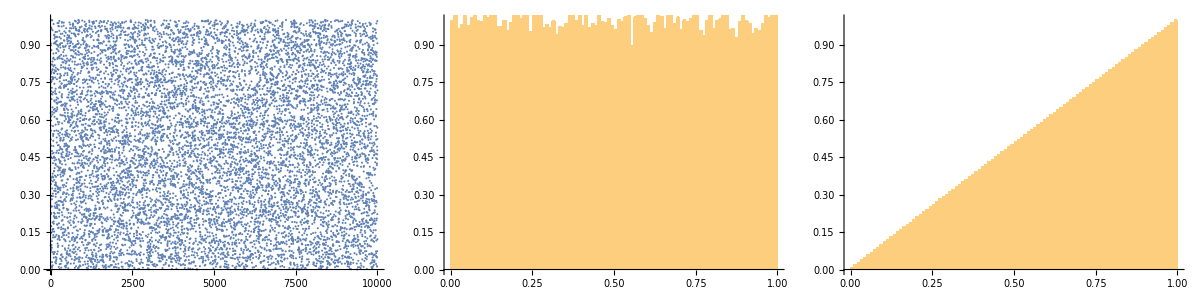

0.438176265

0.2287662507968

```mathematica
Clear[xi];
xi=RandomReal[1,100000,WorkingPrecision->16];
Grid[{{ListPlot[xi[[1;;10000]],Joined->False,PlotRange->{{0,10000},{0,1}},AspectRatio->1],Histogram[xi,100,"PDF",PlotRange->{{0,1},{0,1}},AspectRatio->1],
Histogram[xi,100,"CDF",PlotRange->{{0,1},{0,1}},AspectRatio->1]}}]
AndersonDarlingTest[xi,UniformDistribution[]]
PearsonChiSquareTest[xi,UniformDistribution[]]
```

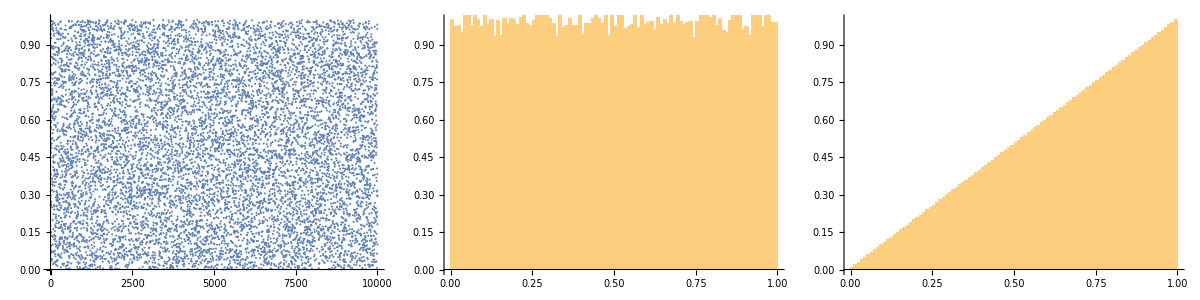

0.3578103973277

0.4350430229321655

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=ReadList["randoms19937.tst",Real];
Grid[{{ListPlot[xi[[1;;10000]],Joined->False,PlotRange->{{0,10000},{0,1}},AspectRatio->1],Histogram[xi,100,"PDF",PlotRange->{{0,1},{0,1}},AspectRatio->1],
Histogram[xi,100,"CDF",PlotRange->{{0,1},{0,1}},AspectRatio->1]}}]
AndersonDarlingTest[xi,UniformDistribution[]]
PearsonChiSquareTest[xi,UniformDistribution[]]
```

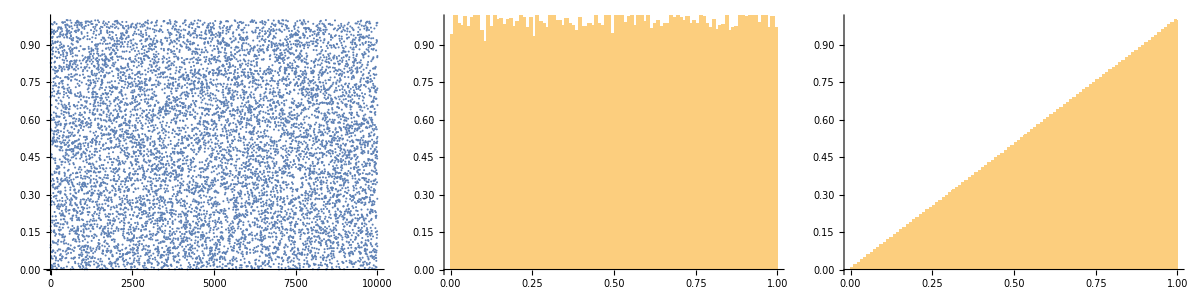

0.3946472270181

0.76678414944464504

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=ReadList["randoms19937x64.tst",Real];
Grid[{{ListPlot[xi[[1;;10000]],Joined->False,PlotRange->{{0,10000},{0,1}},AspectRatio->1],Histogram[xi,100,"PDF",PlotRange->{{0,1},{0,1}},AspectRatio->1],
Histogram[xi,100,"CDF",PlotRange->{{0,1},{0,1}},AspectRatio->1]}}]
AndersonDarlingTest[xi,UniformDistribution[]]
PearsonChiSquareTest[xi,UniformDistribution[]]
```